```mathematica
ClearAll[Fdiv];
SetAttributes[Fdiv,HoldAll];
Off[NIntegrate::izero];
Off[General::stop];
```

```mathematica
WorkingPrec = 15;
MaxRec = 50;
integralLowerX=0.05;
integralUpperX = 0.4;
```

```mathematica
Fdiv[Adensity_,Bdensity_,f_]:= Module[{adivbyb,functiontointegrate},
adivbyb[x_]:= Adensity[x] / Bdensity[x];
functiontointegrate[x_] := Expand[Bdensity[x]*Composition[f,adivbyb][x]];
Return  [NIntegrate[functiontointegrate[x], {x, integralLowerX,integralUpperX},WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec]];
]

(* NIntegrate[Expand[Bdensity[x]*Composition[f,Adensity[x]/Bdensity[x]][x]], {x,-2, 2}]; *)
```

```mathematica
(* EXP1: All distances except Wasserstein.  *)
integralLowerX=0.05;
integralUpperX = 0.4;
means = Subdivide[0.15,0.32, 20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[1]],std],NormalDistribution[means[[13]],std/2]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std],NormalDistribution[means[[17]],std/2]}];
Ddist :=MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[17]],std],NormalDistribution[means[[5]],std/2]}];

Adensity[x_] := PDF[Adist,x];
Bdensity[x_] := PDF[Bdist,x];
Cdensity[x_] := PDF[Cdist,x];
Ddensity[x_] := PDF[Ddist,x];

Acum[x_] :=  CDF[Adist,x];
Bcum[x_] :=  CDF[Bdist,x];
Ccum[x_] :=  CDF[Cdist,x];
Dcum[x_] :=  CDF[Ddist,x];
```

```mathematica
(* EXP2: Wasserstein distance *)
integralLowerX=0.05;
integralUpperX = 0.4;
means = Subdivide[0.15,0.32, 10];
std = 0.005;
nearnessAD1 = 0.85;
nearnessAD2 =0.25;

Adist := MixtureDistribution[{1.2,1.0},{NormalDistribution[(1-nearnessAD1)*means[[1]] + nearnessAD1*(means[[3]]),std],NormalDistribution[(1-nearnessAD2)*means[[4]] + nearnessAD2*(means[[6]]),std]}];
Bdist := MixtureDistribution[{1.0,1.0},{NormalDistribution[means[[3]],std],NormalDistribution[means[[6]],std]}];
Cdist := MixtureDistribution[{1.0,1.0},{NormalDistribution[means[[4]],std],NormalDistribution[means[[5]],std]}];
Ddist :=MixtureDistribution[{1.0,1.2},{NormalDistribution[(1-nearnessAD2)*means[[5]] + nearnessAD2*(means[[3]]),std],NormalDistribution[(1-nearnessAD1)*means[[8]] + nearnessAD1*(means[[6]]),std]}];


Adensity[x_] := PDF[Adist,x];
Bdensity[x_] := PDF[Bdist,x];
Cdensity[x_] := PDF[Cdist,x];
Ddensity[x_] := PDF[Ddist,x];

Acum[x_] :=  CDF[Adist,x];
Bcum[x_] :=  CDF[Bdist,x];
Ccum[x_] :=  CDF[Cdist,x];
Dcum[x_] :=  CDF[Ddist,x];
```

```mathematica
(* EXP3: See the variation to translation etc. *)
```

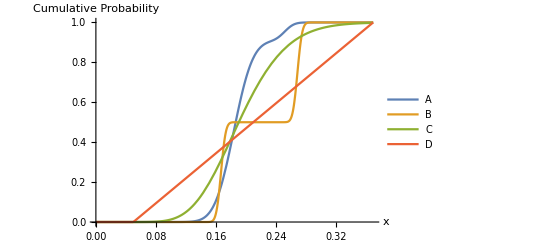

```mathematica
(* Original *)
integralLowerX=0.05;
integralUpperX = 0.37;

means = Subdivide[0.15,0.32,20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std*4],NormalDistribution[means[[13]],std*2]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := GammaDistribution[15,0.013];
uniformLower =integralLowerX;
uniformUpper = integralUpperX;
Ddist :=UniformDistribution[{uniformLower, uniformUpper}];

Adensity[x_] := PDF[Adist,x];
Bdensity[x_] := PDF[Bdist,x];
Cdensity[x_] := PDF[Cdist,x];
Ddensity[x_] := PDF[Ddist,x];

Acum[x_] :=  CDF[Adist,x];
Bcum[x_] :=  CDF[Bdist,x];
Ccum[x_] :=  CDF[Cdist,x];
Dcum[x_] :=  CDF[Ddist,x];

plot = Plot[{Acum[x],Bcum[x],Ccum[x],Dcum[x]},{x, 0.0,0.37}, PlotLegends->{"A","B","C", "D"}, PlotRange->Full, AxesLabel->{"x","Cumulative Probability"}]
```

```mathematica
(* Translation *)

integralLowerX=0.05;
integralUpperX = 0.37;

lambda = 0.025;



means = Subdivide[0.15,0.32,20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std*4],NormalDistribution[means[[13]],std*2]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := GammaDistribution[15,0.013];
uniformLower =integralLowerX;
uniformUpper = integralUpperX;
Ddist :=UniformDistribution[{uniformLower, uniformUpper}]; (*No need to change the bounds here, we change the distribution in *)

Adensity[x_] := PDF[TransformedDistribution[u+lambda,u\[Distributed]Adist],x];
Bdensity[x_] := PDF[TransformedDistribution[u+lambda,u\[Distributed]Bdist],x];
Cdensity[x_] := PDF[TransformedDistribution[u+lambda,u\[Distributed]Cdist],x];
Ddensity[x_] := PDF[TransformedDistribution[u+lambda,u\[Distributed]Ddist],x];

Acum[x_] :=  CDF[TransformedDistribution[u+lambda,u\[Distributed]Adist],x];
Bcum[x_] :=  CDF[TransformedDistribution[u+lambda,u\[Distributed]Bdist],x];
Ccum[x_] :=  CDF[TransformedDistribution[u+lambda,u\[Distributed]Cdist],x];
Dcum[x_] :=  CDF[TransformedDistribution[u+lambda,u\[Distributed]Ddist],x];

integralLowerX = integralLowerX + lambda; (* change this after D (uniform) is defined, otherwise we do not define the same prob dist*)
integralUpperX = integralUpperX + lambda;
```

```mathematica
(* Dilatation *)

integralLowerX=0.05;
integralUpperX = 0.37;

lambda = 1.12;



means = Subdivide[0.15,0.32,20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std*4],NormalDistribution[means[[13]],std*2]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := GammaDistribution[15,0.013];
uniformLower =integralLowerX;
uniformUpper = integralUpperX;
Ddist :=UniformDistribution[{uniformLower, uniformUpper}];

Adensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Adist],x];
Bdensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Bdist],x];
Cdensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Cdist],x];
Ddensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Ddist],x];

Acum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Adist],x];
Bcum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Bdist],x];
Ccum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Cdist],x];
Dcum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Ddist],x];

integralLowerX = integralLowerX * lambda; (* change this after D (uniform) is defined, otherwise we do not define the same prob dist*)
integralUpperX = integralUpperX * lambda;
```

```mathematica
(* Inverse *)

integralLowerX=0.05;
integralUpperX = 0.37;

lambda = -1.0;

means = Subdivide[0.15,0.32,20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std*4],NormalDistribution[means[[13]],std*2]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := GammaDistribution[15,0.013];
uniformLower =integralLowerX;
uniformUpper = integralUpperX;
Ddist :=UniformDistribution[{uniformLower, uniformUpper}];

Adensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Adist],x];
Bdensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Bdist],x];
Cdensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Cdist],x];
Ddensity[x_] := PDF[TransformedDistribution[u*lambda,u\[Distributed]Ddist],x];

Acum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Adist],x];
Bcum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Bdist],x];
Ccum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Cdist],x];
Dcum[x_] :=  CDF[TransformedDistribution[u*lambda,u\[Distributed]Ddist],x];

temp = integralUpperX * lambda; (* if we multiply by -1, the lower bound is the upper bound*)
integralUpperX = integralLowerX * lambda;
integralLowerX = temp;
```

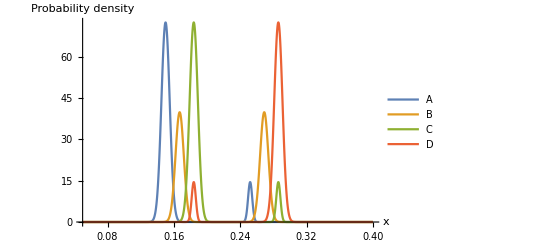

densityplot.pdf

```mathematica
plot = Plot[{Adensity[x],Bdensity[x],Cdensity[x],Ddensity[x]},{x, integralLowerX,integralUpperX},  PlotLegends->{"A","B","C", "D"}, PlotRange->Full, AxesLabel->{"x","Probability density"}]
Export["densityplot.pdf",plot]
```

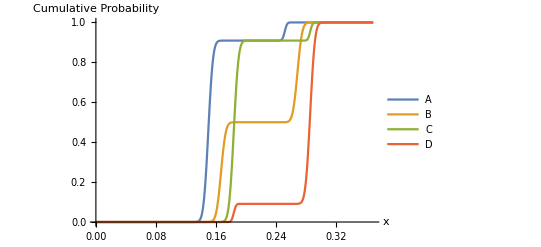

cumulativedensityplot.pdf

```mathematica
plot = Plot[{Acum[x],Bcum[x],Ccum[x],Dcum[x]},{x, 0.0,0.37}, PlotLegends->{"A","B","C", "D"}, PlotRange->Full, AxesLabel->{"x","Cumulative Probability"}]
Export["cumulativedensityplot.pdf",plot]
```

```mathematica
fKL[x_]:= x * Log[x]
fJS[x_] := x * Log[2*x / (x +1)]+ Log[2/(x+1)]
fTV[x_]:= 0.5*Abs[x -1]
fHellsquared[x_]:= (1 - Sqrt[x])^2
```

```mathematica
Fdiv[Adensity,Ddensity,fHellsquared]
Fdiv[Cdensity,Adensity,fTV]
```

1.99990095033957

0.999387401333945

```mathematica
ffunctions = {fKL,fJS,fHellsquared,fTV};
distributions={Adensity,Bdensity,Cdensity,Ddensity};
cumdistributions={Acum,Bcum,Ccum,Dcum};
listOfMatrices=ConstantArray[0,{7,4,4}];
WriteString["stdout","dist1,dist2,KL, JS, Helligner, Total Variation,Total variation altern., Wasserstein, Wasserstein without abs, "]
For[j=0,j<4,j++,
For[k=0,k<4,k++,
distcurrent1 = distributions[[j+1]];
distcurrent2 = distributions[[k+1]];
cumdistcurrent1 = cumdistributions[[j+1]];
cumdistcurrent2 = cumdistributions[[k+1]];
WriteString["stdout","\n",distcurrent1, ",", distcurrent2, ","];
For[i=0,i<2,i++,
fcurrent = ffunctions[[i+1]];
res = Round[Fdiv[distcurrent1,distcurrent2,fcurrent],0.001];
listOfMatrices[[i+1,j+1,k+1]] =res;
WriteString["stdout", ToString[res], "," ];
];
(*Helligner*)
fcurrent = ffunctions[[3]];
res = Round[Sqrt[Fdiv[distcurrent1,distcurrent2,fcurrent]], 0.001];
listOfMatrices[[3,j+1,k+1]] =res;
WriteString["stdout", ToString[res], "," ];

(*TV *)
fcurrent = ffunctions[[4]];
res = Round[Fdiv[distcurrent1,distcurrent2,fcurrent],0.001];
listOfMatrices[[4,j+1,k+1]] =res;
WriteString["stdout", ToString[res], "," ];

(* TV alt*)
res = Round[NIntegrate[0.5*Abs[distcurrent1[x] - distcurrent2[x]],{x,integralLowerX,integralUpperX}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec],0.001];
WriteString["stdout", ToString[res], "," ];
listOfMatrices[[5,j+1,k+1]] = res;

(*Wasserstein*)
res = Round[NIntegrate[Abs[cumdistcurrent1[x] - cumdistcurrent2[x]],{x, integralLowerX,integralUpperX}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec], 0.001];
listOfMatrices[[6,j+1,k+1]] =res;
WriteString["stdout", ToString[res],","];

(*Wasserstein without abs*)
res = Round[NIntegrate[cumdistcurrent1[x] - cumdistcurrent2[x],{x, integralLowerX,integralUpperX}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec], 0.001];
listOfMatrices[[7,j+1,k+1]] =res;
WriteString["stdout", ToString[res]];
];
];
For[i=1,i≤ 7,i++,
Print [{"KL", "JS", "Helligner", "TV", "TV alt", "Wasserstein","Wasserstein without abs","Total variation-alternative computation"}[[i]]];
Print[listOfMatrices[[i]] // MatrixForm]
]
```

dist1,dist2,KL, JS, Helligner, Total Variation,Total variation altern., Wasserstein, Wasserstein without abs, 
Adensity,Adensity,0.,0.,0.,0.,0.,0.,0.
Adensity,Bdensity,6.197,1.216,1.282,0.934,0.934,0.059,0.059
Adensity,Cdensity,28.59,1.385,1.412,0.999,0.999,0.034,0.034
Adensity,Ddensity,88.821,1.386,1.414,1.,1.,0.117,0.117
Bdensity,Adensity,15.407,1.216,1.282,0.934,0.934,0.059,-0.059
Bdensity,Bdensity,0.,0.,0.,0.,0.,0.,0.
Bdensity,Cdensity,15.405,1.216,1.282,0.934,0.934,0.04,-0.025
Bdensity,Ddensity,15.407,1.216,1.282,0.934,0.934,0.059,0.059
Cdensity,Adensity,29.425,1.385,1.412,0.999,0.999,0.034,-0.034
Cdensity,Bdensity,6.197,1.216,1.282,0.934,0.934,0.04,0.025
Cdensity,Cdensity,0.,0.,0.,0.,0.,0.,0.
Cdensity,Ddensity,2.646,0.831,0.986,0.818,0.818,0.083,0.083
Ddensity,Adensity,88.821,1.386,1.414,1.,1.,0.117,-0.117
Ddensity,Bdensity,6.197,1.216,1.282,0.934,0.934,0.059,-0.059
Ddensity,Cdensity,2.646,0.831,0.986,0.818,0.818,0.083,-0.083
Ddensity,Ddensity,0.,0.,0.,0.,0.,0.,0.

KL

(0. | 6.197 | 28.59 | 88.821
15.407 | 0. | 15.405 | 15.407
29.425 | 6.197 | 0. | 2.646
88.821 | 6.197 | 2.646 | 0.)

JS

(0. | 1.216 | 1.385 | 1.386
1.216 | 0. | 1.216 | 1.216
1.385 | 1.216 | 0. | 0.831
1.386 | 1.216 | 0.831 | 0.)

Helligner

(0. | 1.282 | 1.412 | 1.414
1.282 | 0. | 1.282 | 1.282
1.412 | 1.282 | 0. | 0.986
1.414 | 1.282 | 0.986 | 0.)

TV

(0. | 0.934 | 0.999 | 1.
0.934 | 0. | 0.934 | 0.934
0.999 | 0.934 | 0. | 0.818
1. | 0.934 | 0.818 | 0.)

TV alt

(0. | 0.934 | 0.999 | 1.
0.934 | 0. | 0.934 | 0.934
0.999 | 0.934 | 0. | 0.818
1. | 0.934 | 0.818 | 0.)

Wasserstein

(0. | 0.059 | 0.034 | 0.117
0.059 | 0. | 0.04 | 0.059
0.034 | 0.04 | 0. | 0.083
0.117 | 0.059 | 0.083 | 0.)

Wasserstein without abs

(0. | 0.059 | 0.034 | 0.117
-0.059 | 0. | -0.025 | 0.059
-0.034 | 0.025 | 0. | 0.083
-0.117 | -0.059 | -0.083 | 0.)